# Vaje

## Naloga 1

Obravnavaj met žogice iz višine H v smeri vektorja v0 = {v0x, v0y}.Upoštevaj gravitacijski pospešek g = 9.81 m/s2.Pomagaj si z naslednjimi koraki :

Obravnavaj problem v ravnini, kjer je os x smer meta, os y pa predstavlja višino. Sestavi vektorsko (2D) funkcijo v[t_], ki za dan čas t izračuna vektor hitrosti pri metu.Izberi naslednje parametre :

```mathematica
v0={10,3};
GG=9.81;
H=10;
a ={0,-GG};
x0 ={0,H};
v[t_] := {v0 [[1]],v0[[2]] - GG*t}
v[t_] := v0 + a *t
v[1]
```

{10,-6.81}

Vemo, da velja x (t) = x (0) + R t0v (t) dt.Če veš, da je x0 = {0, H}, sestavi še vektorsko funkcijo X[t_], ki vrne položaj žogice ob času t.

```mathematica
X[t_] := x0 + v0 * t + (a * t^2)/2
X[1]
```

{10,8.095}

Sestavi funkcijo SlikaTocke[t_], ki nariše žogo kot točko.Velikost točke naj bo 3 % slike.

```mathematica
SlikaTocke[t_] :={PointSize[0.03],Point[X[t]]}

Manipulate[Graphics[SlikaTocke[t],Axes->True, PlotRange->{{0,30},{0,30}}, AspectRatio->Automatic],{t,0,1.766035}]
SlikaVektorja[t_] := {Arrowheads[0.05], Arrow[{X[t], X[t]+v[t]}]}
```

Sestavi funkcijo SlikaVektorja[t_], ki nariše vektor hitrosti iz točke.Uporabi grafični objekt
Arrow.Debelina črte naj bo 0, 5 % velikosti slike.

```mathematica
SlikaVektorja[t_] := {Arrowheads[0.05], Arrow[{X[t], X[t]+v[t]}]}

Manipulate[Graphics[{SlikaTocke[t] ,SlikaVektorja[t]},Axes->True, PlotRange->{{0,30},{0,30}}, AspectRatio->Automatic],{t,0,1.076}]
```

Nariši sliko žoge in vektorja po eni sekundi.Na sliki naj se nariše koordinatni sistem, os x
nastavi na interval[−1, 25], os y pa na interval[−5, 15].Velikosti enot na obeh oseh naj bosta
enaki (Namig : preveri delovanje naslednjih opcij v objektu Graphics : Axes, PlotRange in AspectRatio).

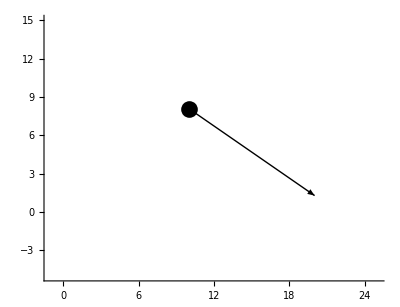

```mathematica
Graphics[{SlikaTocke[1] ,SlikaVektorja[1]},Axes->True, PlotRange->{{-1,25},{-5,15}}, AspectRatio->Automatic]
```

S pomočjo funkcije Manipulate naredi animacijo leta žoge.Čas t premikaj o 0 do 5 s.

```mathematica
Manipulate[Graphics[{SlikaTocke[t] ,SlikaVektorja[t]},Axes->True, PlotRange->{{0,80},{-150,20}}, AspectRatio->Automatic],{t,0,5}]
```

Izračunaj čas padca žoge. Izračunaj še vrednost v smeri x, kjer žoga pade.

```mathematica
Y[t_] := (H + v0 * t) - (GG * t^2)/2
SamoY[{x_,y_}] := y 
rez = Solve[SamoY[Y[t]]== 0,t];
rez = SamoY[rez]
Y[1.766035031964932]
```

{t→1.76604}

{12.3622,3.55271×10^-15}

Izračunaj čas doseganja največje višine leta ter maksimalno višino.

```mathematica
Hitrost = √(v0[[1]]^2+v0[[2]]^2);
casLetaDoNajvišjeTočke = (2*Hitrost*sinkot)/(GG * 2)
sinkot =SamoY[v0]/Hitrost //N ;
MaksimalnaVišina = (Hitrost^2* sinkot^2)/(2*GG)+ H
```

0.30581

10.4587

Uporabi izračuna iz zgornjih dveh točk tako, da bo območje izrisa čimbolj primerno (na osi x od - 1 do malce več kot lokacija padca; na osi y pa naj bo od nekaj pod ničlo do malce več kot maksimalna višina leta; čas animacije naj bo od 0 do trenutka padca.

```mathematica
domet  =Hitrost^2 *Sin[2*ArcSin[sinkot]]/GG + H;
Manipulate[Graphics[{SlikaTocke[t],Arrow[{X[t], X[t]+v[t]}]}, Axes->True, PlotRange->{ {-1, domet +4},{-4, MaksimalnaVišina + 4}}, AspectRatio-> Automatic],{t, 0, casLeta}
]
```

Kakšna je absolutna vrednost hitrosti v trenutku, ko žogica zadene tla?

```mathematica
casLeta= casLetaDoNajvišjeTočke + √((2*MaksimalnaVišina)/GG);
absHitrosti=√((v[casLeta][[1]])^2  + (v[casLeta][[2]])^2)
casLeta
```

1.76604

## Naloga 2

Ravnino podamo v obliki Ravnina[n_, v_], kjer je n normala na ravnino in je v točka na
ravnini.Npr.ravnina, ki gre skozi točko (1, 1, 1) in je pravokotna na glavno diagonalo je r111 = Ravnina[{-1, -1, -1}, {1, 1, 1}].

Sestavi funkcijo Slika[Ravnina[n_, v_]], ki pripravi 3D grafični objekt.Oglej si grafični objekt
Hyperplane.

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}]
Slika[Ravnina[n_,v_]] := Hyperplane[n,v]
```

-Graphics3D-

Sestavi funkcijo Format[r_Ravnina], ki nariše ravnino.Pozor : če definiramo funkcijo Format
na objektih, se ti objekti "sami" izrišejo.

```mathematica
Format[r_Ravnina] := Graphics3D[Slika[r]]
```

Sestavi še priročni funkciji Normala[Ravnina[n_, v_]] in Tocka[Ravnina[n_, v_]], ki vrneta
točko in normalo ravnine.

```mathematica
Normala[Ravnina[n_,v_]] := n
Normala[r111]
```

{-1,-1,-1}

Definiraj koordinatne ravnine rx, ry, rz, ki gredo skozi točko 0 in so njihove normale enotski
vektorji koordinatnih osi.

```mathematica
rx = Ravnina[{1, 0, 0}, {0, 0, 0}];
ry = Ravnina[{0, 1, 0}, {0, 0, 0}];
rz = Ravnina[{0, 0, 1}, {0, 0, 0}];
ravnine = {rx, ry, rz, r111}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Sestavi funkcijo SlikaNormale[Ravnina[n_, v_]], ki vrne grafični objekt slike normale.Uporabi
grafični objekt Arrow.

```mathematica
SlikaNormale[Ravnina[n_,v_]] := Arrow[{v,v+n}]
slikeNormal = Map[SlikaNormale, ravnine];
Graphics3D[{slikeNormal}, PlotRange->{{-1, 2}, {-1,2},{-1,2}}]
```

-Graphics3D-

Nariši vse štiri ravnine rx, ry, rz, r111 na isti sliki skupaj z normalami

```mathematica
slikeRavnin = Map[Slika, ravnine];
Graphics3D[{slikeRavnin, slikeNormal}, PlotRange->{{-1, 4}, {-1, 4},{-1, 4}}]
```

-Graphics3D-

Sestavi funkcijo Enacba[Ravnina[n_, v_]], ki vrne enačbo ravnine.

```mathematica
Enacba[Ravnina[n_, v_]]:=Module[{x, y, z,d},
d =n[[1]] v[[1]] + n[[2]] v[[2]] + n[[3]] v[[3]];
n[[1]] x + n[[2]] y+ n[[3]] z == d ]
Enacba[r111]
```

-x$4849-y$4849-z$4849==-3

Sestavi funkcijo ResiSistem[sistem_List], ki za dan sistem treh enačb v spremenljivkah x, y
in z vrne točko rešitve.Predpostavi, da je sistem takšen, da vrne samo eno rešitev.

Sestavi funkcijo Presecisca[ravnine_List], ki za dan seznam ravnin poišče vse podmnožice
velikosti 3 in potem poišče vse preseke treh ravnin iz teh podmnožic.Uporabi funkcijo Subset
ter funkciji iz prejšnjih dveh nalog.

Sestavi funkcijo Vsebuje[Ravnina[n_, v_], x_, y_, z_, eps_: 0.000001], ki s toleranco
10 − 6 natančno ugotovi, ali je točka v ravnini.Uporabi definicijo ravnine~n·(~r0 − ~r) = 0, kjer za vrednost na levi strani namesto enačenja z nič dopuščaš odmik za .0f.

Sestavi funkcijo Trikotnik[r_Ravnina, tocke_List], ki za dano ravnino in seznam točk nariše
trikotnik na točkah, ki so vsebovane v ravnini.Predpostavimo, da bodo izmed točk podanih v
seznamu točke, vedno natanko tri na ravnini - katere tri pa moramo izračunati.Izračunaj še vsa
presečišča štirih ravnin (uporabi zgornjo funkcijo) ter trikotnik za ravnino rx.

Sestavi funkcijo Trikotnik[r_Ravnina, tocke_List], ki za dano ravnino in seznam točk nariše
trikotnik na točkah, ki so vsebovane v ravnini.Predpostavimo, da bodo izmed točk podanih v
seznamu točke, vedno natanko tri na ravnini - katere tri pa moramo izračunati.Izračunaj še vsa
presečišča štirih ravnin (uporabi zgornjo funkcijo) ter trikotnik za ravnino rx.

## Naloga 3

Izberi si neko 3D telo in ga nariši s pomočjo točk in poligonov. Enostavni primeri so kocke, kvadri. Bolj napredni so piramide, prizme, prerezane piramide. . . Bodite izvirni in narišite nekaj lepega.Narišite tudi normalo nad eno ploskvijo, ki gleda ven iz telesa iz težišča ploskve.

```mathematica
AA={0,0,0}; BB ={2,0,0}; CC ={2,2,0}; DD ={0,2,0}; EE ={1,1,2};
```

```mathematica
Tocke[AAA_,BBB_,CCC_,DDD_,EEE_] := {AAA,BBB,CCC,DDD,EEE}
Piramida[tocke_] := Pyramid[tocke]
tocke = Tocke[AA,BB,CC,DD,EE]
piramida = Piramida[tocke]
```

{{0,0,0},{2,0,0},{2,2,0},{0,2,0},{1,1,2}}

Pyramid[{{0,0,0},{2,0,0},{2,2,0},{0,2,0},{1,1,2}}]

```mathematica
normala1 = {1,1,0} 
normala2 = {1,1,3}
Graphics3D[piramida,Arrow[{normala1,normala2}]]
```

{1,1,0}

{1,1,3}

-Graphics3D-